# Code

## Mathematical Model of a Personalized Neoantigen Cancer Vaccine and the Human Immune System: Evaluation of Efficacy

Author: Marisabel Rodriguez Messan, PhD

U.S. Food and Drug Administration, Silver Spring, MD 20993

This code solves a non-linear system of ODE’s with scheduled constant vaccine doses. 
The code is designed to use patient-specific information such as HLA affinities, peptide-vaccine concentration,and  initial tumor cell count (or size).
The output simulations show the total number of activated T-cells and  tumor cell count throughout treatment.

To run this code (Shift+Enter to execute each cell):
1. Initialize
2. Import data (Patients_HLA_BA.xlsx, Tcellscounts.xlsx, and Best-fit_param.xlsx)
3. Estimate patients’ tumor size 
4. Now you can solve the ODE system

## Initialization

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Marisabel.Rodriguez\OneDrive - FDA\CancerVax\SUBMISSION\Code

Settings for nice plot legends

```mathematica
legendoptions={LabelStyle->{Bold,Black,16},LegendMarkerSize->{25,30}};
```

## Importing Data

Melanoma patients (6 total)

```mathematica
dataNetMHCIIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",2},"HeaderLines"->1];
dataNetMHCIpanAll=Import["Patients_HLA_BA.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
TcellsPatientData = Import["Tcellscounts.xlsx",{"XLSX","Data",1},"HeaderLines"-> 1];
ParmEstim=Import["Best-fit_param.xlsx",{"XLSX","Data",1},"HeaderLines"->1];
```

### Cleaning and organizing patient data

#### Melanoma patients

If imported as “Data”, Grid lets you visualize as a table

```mathematica
Grid[TcellsPatientData];
```

Choose all rows and columns 1, 2, 8, 9

```mathematica
FullDose = TcellsPatientData[[All,{1,2,8,9}]];
```

Multiply 3rd column by 1.42857 x10^6

```mathematica
FullDoseScaleUp = FullDose/.{x_,y_,z_,w_}->{x,y,(1.42857*^6)*z,w}; (*Spot-forming cells per 10^6; there are ~1.42857x10^12 PBMCs*)
```

Group by Patients; select a specific patient

```mathematica
byPatient = GatherBy[FullDoseScaleUp,#[[2]]&];
```

```mathematica
patient1 = Select[FullDoseScaleUp,#[[2]]==1&];
patient2 = Select[FullDoseScaleUp,#[[2]]==2&];
patient3 = Select[FullDoseScaleUp,#[[2]]==3&];
patient4 = Select[FullDoseScaleUp,#[[2]]==4&];
patient5 = Select[FullDoseScaleUp,#[[2]]==5&];
patient6 = Select[FullDoseScaleUp,#[[2]]==6&];
```

## Initial tumor size estimation

Cell count (volume of a sphere, minus void volume, times 100,000)

```mathematica
Vc[d_]:=((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)
```

Estimation of diameter size given cell count. Input number of cells; Output diameter in millimeters

```mathematica
Diam[cells_]:=Solve[((4 Pi)/3*(d/2)^3)(0.7405)(1*^5)==cells,d,Reals]
```

```mathematica
Diam[3.3*^8]
```

```mathematica
tumorFun =Flatten[Table[NDSolve[{T'[τ]==0.004(1-T[τ]/(1.45*^10))T[τ],T[0]==t0},{T},{τ,0,180}],{t0,{851056,7.27*^8,608728,726984,500165,7.27*^8}}]];
```

```mathematica
Grid[{{Text[Style["Patient",Bold]],Text[Style["Stage by tumor\ntickness",Bold]],Text[Style["Tumor cell count\nBEFORE sugery",Bold]],Text[Style["Tumor cell count\nAFTER sugery (5%)",Bold]],Text[Style["Time lag (days)",Bold]],Text[Style["Tumor cell count\nat the beginning\nof treatment",Bold]]},
{1,Text["T3 (N3M0)"],Vc[4]+3*Vc[5],(Vc[4]+3*Vc[5])*.05,120,T[τ]/.tumorFun[[1]]/.τ->120},
{2,Text["T4 (N0M1b)"],Vc[5]+3*Vc[50],(Vc[5]+3*Vc[50])*.05,120,T[τ]/.tumorFun[[2]]/.τ->120},
{3,Text["T3 (N2M0)"],Vc[4]+2*Vc[5],(Vc[4]+2*Vc[5])*.05,165,T[τ]/.tumorFun[[3]]/.τ->165},
{4,Text["T4 (N2M0)"],Vc[5]+2*Vc[5],(Vc[5]+2*Vc[5])*.05,180,T[τ]/.tumorFun[[4]]/.τ->180},
{5,Text["T2 (N2M0)"],Vc[2]+2*Vc[5],(Vc[2]+2*Vc[5])*.05,135,T[τ]/.tumorFun[[5]]/.τ->135},
{6,Text["T2 (N0M1b)"],Vc[2]+3*Vc[50],(Vc[2]+3*Vc[50])*.05,105,T[τ]/.tumorFun[[6]]/.τ->105}},Frame->All,Background->{None,{LightBlue}},Spacings->{Automatic,.8},ItemStyle->Directive[FontSize->14],Alignment->{Center,Center}]
```

Patient | Stage by tumor
tickness | Tumor cell count
BEFORE sugery | Tumor cell count
AFTER sugery (5%) | Time lag (days) | Tumor cell count
at the beginning
of treatment
1 | T3 (N3M0) | 1.70211×10^7 | 851056. | 120 | 1.37532×10^6
2 | T4 (N0M1b) | 1.45445×10^10 | 7.27227×10^8 | 120 | 1.13968×10^9
3 | T3 (N2M0) | 1.21746×10^7 | 608728. | 165 | 1.17772×10^6
4 | T4 (N2M0) | 1.45397×10^7 | 726984. | 180 | 1.49346×10^6
5 | T2 (N2M0) | 1.00033×10^7 | 500165. | 135 | 858265.
6 | T2 (N0M1b) | 1.454×10^10 | 7.27×10^8 | 105 | 1.07825×10^9

## Plots of Melanoma Patient Data (T-cell responses)

### Plots by Patient and All Patients

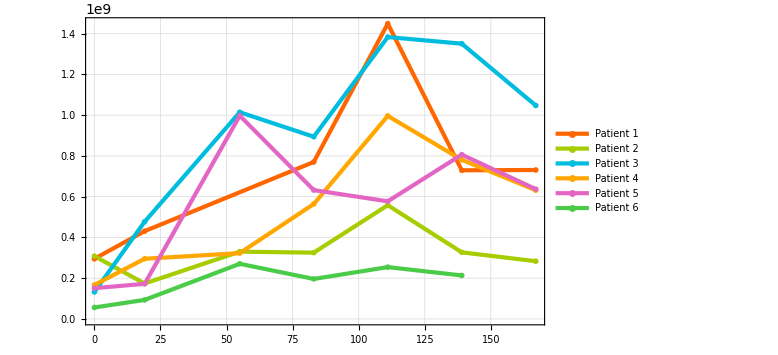

```mathematica
ListLinePlot[#[[All,{1,3}]]&/@byPatient,PlotTheme->{"NeonColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 1","Patient 2","Patient 3","Patient 4","Patient 5","Patient 6"},LegendFunction->(Framed[#,RoundingRadius->5]&)],Below],ImageSize->Large]
```

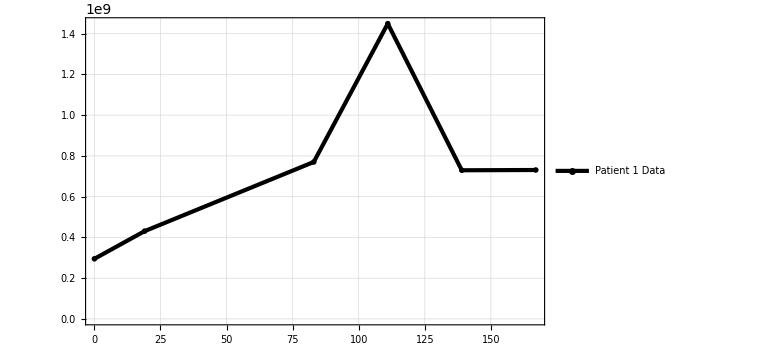

```mathematica
P1Plot=ListLinePlot[patient1[[All,{1,3}]],PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 1 Data"},legendoptions],{0.17,0.88}],ImageSize->Large]
```

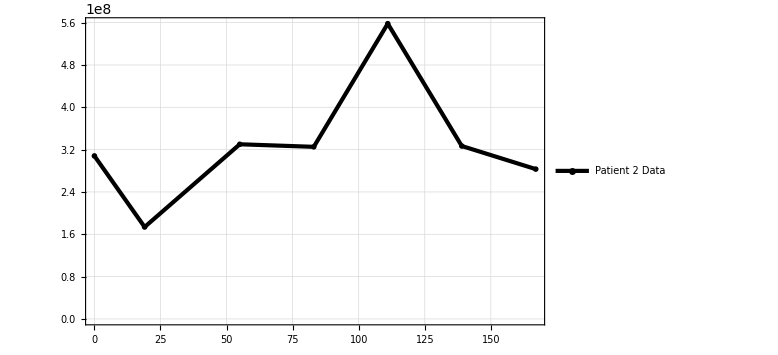

```mathematica
P2Plot=ListLinePlot[patient2[[All,{1,3}]],PlotRange->Full,PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 2 Data"},legendoptions],{0.17,0.88}],ImageSize->Large]
```

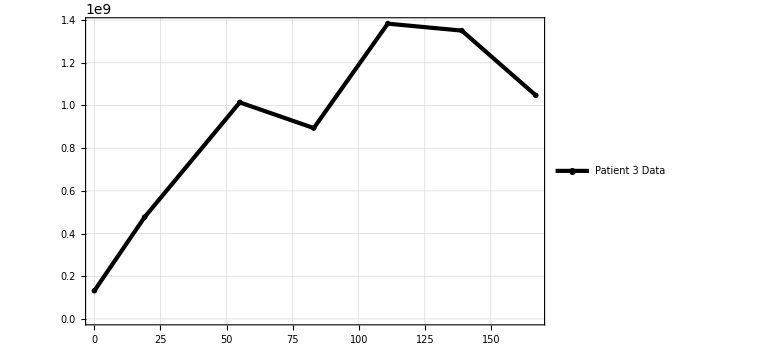

```mathematica
P3Plot=ListLinePlot[patient3[[All,{1,3}]],PlotRange->Full,PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 3 Data"},legendoptions],{0.16,0.9}],ImageSize->Large](*Patient 3*)
```

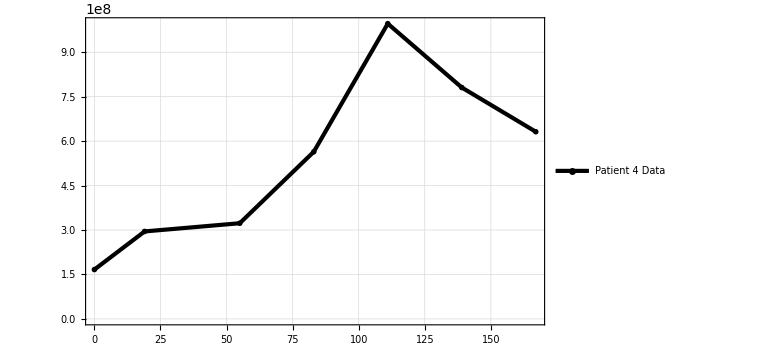

```mathematica
P4Plot=ListLinePlot[patient4[[All,{1,3}]],PlotRange->Full,PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 4 Data"},legendoptions],{0.17,0.9}],ImageSize->Large](*Patient 4*)
```

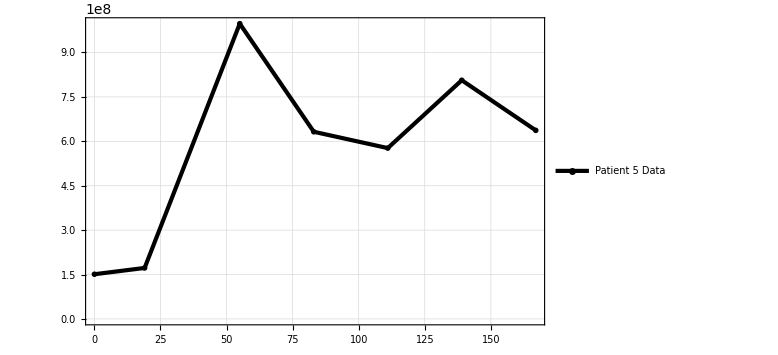

```mathematica
P5Plot=ListLinePlot[patient5[[All,{1,3}]],PlotRange->Full,PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 5 Data"},legendoptions],{0.8,0.25}],ImageSize->Large]
```

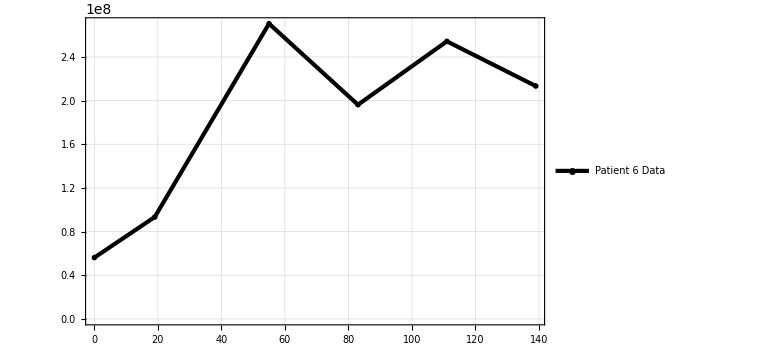

```mathematica
P6Plot=ListLinePlot[patient6[[All,{1,3}]],PlotRange->Full,PlotTheme->{"GrayColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 6 Data"},legendoptions],{0.17,0.9}],ImageSize->Large]
```

```mathematica
P1345Plot=ListLinePlot[{patient1[[All,{1,3}]],patient3[[All,{1,3}]],patient4[[All,{1,3}]],patient5[[All,{1,3}]]},PlotRange->Full,PlotTheme->{"NeonColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 1","Patient 3","Patient 4","Patient 5"}],Above],ImageSize->Large];
```

```mathematica
P26Plot=ListLinePlot[{patient2[[All,{1,3}]],patient6[[All,{1,3}]]},PlotRange->Full,PlotTheme->{"NeonColor","Detailed","ThickLines"},PlotMarkers->"OpenMarkersThick",LabelStyle->Directive[Black,Bold, 16],FrameStyle->Directive[Black],PlotLegends->Placed[LineLegend[{"Patient 2","Patient 6"}],Above],ImageSize->Large];
```

## Solving the non-linear ODE system

```mathematica
Manipulate[
Module[{NA,injectiontimes, Dosea, Dosep,αd,αp,αpE,δM,Ka,Λ,rD,Kdc,Ktc4,Ktc8,Kt,KpM1,KpM2,a1,a2,b1,b2,c,cc,d1,d2,g,μ1,μ2,μ3,σNh,σNc,ρ1,ρ2,r,s1,s2,λ,kin,kext,kon1,kon2,koff,koffj,VE,VDC,Vsc,βM,βpM,βp,Fp1,Fp2,Vax,AffinbyPatientI,AffinbyPatientII,patientHLAAffinI ,patientHLAAffinII,KDsI,KDsII,KDeffI,KDeffII,Φ1,Φ2,p0,Ad0,Di0,Dm0,Ncd40,Ncd80,Acd40,Acd80,T0,pE0,ME0,MEj0,jend,kend, n,eqns,ab,bc,peptide,adjuv,DCi,DCm,Ncd4p,Ncd8p,Acd4p,Acd8p,tumor,EndoPep,MEjp,MEkp,pMEjp,pMEkp,pMjp,pMkp,Mjp,Mkp,P,v},

P=patient;
v=vaccine;
(*a1=a1o;a2=a2o;c=c1;cc=c2;ρ1=rho1;ρ2=rho2;
d1=d1o;d2= d2o;λ=λo;s1=s1o;s2=s2o;Fp1=fp1;Fp2=fp2;*)(*δ=delta;*)(*Λ=Lambd;*)
(*σNc=aNc;σNh=aNh;*)(*μ1=mu1;μ2=mu2;*)(*αd=ado;αp=αpo;αpE=apEo;*)

If[patient==1,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];

If[patient==2,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];

If[patient==3,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];

If[patient==4,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];

If[patient==5,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];

If[patient==6,{Fp1=ParmEstim[[1,patient+1]],Fp2=ParmEstim[[2,patient+1]],a1=ParmEstim[[3,patient+1]],a2=ParmEstim[[4,patient+1]],c=ParmEstim[[5,patient+1]],cc=ParmEstim[[6,patient+1]],d1=ParmEstim[[7,patient+1]],s1=ParmEstim[[8,patient+1]],s2=ParmEstim[[9,patient+1]],λ=ParmEstim[[10,patient+1]],ρ1=ParmEstim[[11,patient+1]],ρ2=ParmEstim[[12,patient+1]]}];


injectiontimes = {0,3,7,14,21,83,139}; 
NA=6.0221367*^23; (*Avogadro's constant*)
Dosea=0.5*^3; (*adjuvant concentration per vaccine in mg/L*)
Dosep= {119340,120030,109570,116570,110860,111820};  (*peptide dose in pmols; Used https://www.bioinformatics.org/sms/prot_mw.html to calculate Protein Molecular weight; To convert from weight to moles: http://molbiol.edu.ru/eng/scripts/01_04.html*)
αp=0.28;αd=.5;αpE=70;(*αd=.2;*)

Λ=3.75;(*0.363;*)
δM=.11;(*Immature (.09) and mature DC death rate*)
rD=3;(*1.12;*) (*max maturation rate - DCs (see DC maturation section below-fitted)*)
Ka=10;(*4;*) (*mg/L - adjuvant concentration at which immature Dc activation rate is 50% max; value from fitting (see DC maturation section below) *)
Kdc=2.5*^7;  (*DC Carrying capacity; Unit: # cells *)

b1=0.15;b2=0.12;
Ktc4= 6*^11;  (*T-Cells Carrying capacity; Unit: # cells*)
Ktc8=2.57*^11;  (*CD8 T-Cells Carrying capacity; Unit: # cells *)
μ1=0.031;μ2=0.022;
μ3=0.0029;
(*ρ1=1.51;ρ2=2.6;*)(*1*^-5;*)
σNc=3;σNh=1.5;
KpM1=400;KpM2=400;

Kt=1.45*^10; (*Tumor Carrying capacity Unit: # cells *)
r=0.004;(*0.006;*)(*d1=4.98*^-7;d2=5.1*^-7;*)
(*d1=0.17;d2= 0.1;λ=3;s1=50;s2=50;*)

βp=14.4;
βM=1.663;
βpM=.1663;
VDC=2.5388*^-12; (*https://link.springer.com/article/10.1007/s10928-013-9328-y/tables/2*)
Vsc=4*0.1919;(*;2.75;*)
VE=1*^-14;

(*Input data*)
Vax={3;;15,16;;32,33;;46,47;;60,61;;80,81;;100}; (*6 vaccines, selecting columns that correspond to each vaccine*)
AffinbyPatientI = Select[dataNetMHCIpanAll,#[[1]]==P&]; (*set of HLA's by patient - these are in rows *)
AffinbyPatientII=Select[dataNetMHCIIpanAll,#[[1]]==P&];

(*MHC I molecules*)
KDsI=AffinbyPatientI[[1;;,Vax[[v]]]];(* Calculate KDs for each vaccine and each HLA allotype specific to the patient*)
KDeffI=1/Total[1/Transpose[KDsI]]*1*^3;(*pmol*)
kon1=1.8144*^-2;
koffj=kon1*KDeffI;

(*MHC II molecules*)
KDsII=AffinbyPatientII[[1;;,Vax[[v]]]];  (* Calculate KDs for each column representing an HLA allotype specific to the patient*)
KDeffII=1/Total[1/Transpose[KDsII]]*1*^3; (*pmol*) (*list of KDeffs*)
kon2=8.64*^-3;
koff=kon2*KDeffII; (*list of kOFFs*)

(*MHC I & II molecules*)
kin=14.4;
kext=28.8;
jend=Length[AffinbyPatientI]; (*Define total number of j and k alleles for each patient; j is for alleles in MHC-I and k for alleles in MHC-II*)
kend=Length[AffinbyPatientII]; 
n=jend+kend;

(*INITIAL CONDITIONS*)
p0=0;
Ad0=0;
Di0=1*^7;
Dm0=0;
Ncd40=2.408*^9;(*3*^11;*)
Ncd80=1.032*^9;(*2*^11;*)
Acd40=(*{0,0,0,0,0,0};*){patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]}*.7;(*Mean[{patient2[[1,3]]/2,patient6[[1,3]]/2}];*)(*Mean[{patient1[[1,3]]/2,patient3[[1,3]]/2.,patient4[[1,3]]/2,patient5[[1,3]]/2}];*)
Acd80={patient1[[1,3]],patient2[[1,3]],patient3[[1,3]],patient4[[1,3]],patient5[[1,3]],patient6[[1,3]]}*.3;
T0={T[τ]/.tumorFun[[1]]/.τ->120,T[τ]/.tumorFun[[2]]/.τ->120,T[τ]/.tumorFun[[3]]/.τ->165,T[τ]/.tumorFun[[4]]/.τ->180,T[τ]/.tumorFun[[5]]/.τ->135,T[τ]/.tumorFun[[6]]/.τ->105};
pE0=0;
MEj0={40*^4/2,40*^4/2,20*^4/2,70*^4/2}/NA*1*^12;
ME0={20*^4/2,20*^4/2,10*^4/2,10*^4/2}/NA*1*^12;

pMI = NA* 1*^-12 Sum[pMj[j][t],{j,jend}];
pMII =NA *1*^-12Sum[pM[k][t],{k,kend}];

eqns=Partition[Flatten[Rest[FoldList[(
Flatten[{p[t],Ad[t],Di[t],Dm[t],Ncd4[t],Ncd8[t],Acd4[t],Acd8[t],Tu[t],pE[t],Table[MEj[j][t],{j,jend}],Table[ME[k][t],{k,kend}],
Table[pMEj[j][t],{j,jend}],Table[pME[k][t],{k,kend}],Table[pMj[j][t],{j,jend}],Table[pM[k][t],{k,kend}],Table[Mj[j][t],{j,jend}],Table[M[k][t],{k,kend}]}]/.First@NDSolve[{
Flatten[{
p'[t]==-αp p[t], (*Peptides in a Vaccine*)
Ad'[t]==-αd Ad[t], (*Adjuvant in a Vaccine*)
Di'[t]== Λ Di[t](1-Di[t]/Kdc)-rD(Ad[t]/(Ka+Ad[t]))Di[t],(*Immature DC*)
Dm'[t]==rD(Ad[t]/(Ka+Ad[t]))Di[t] -δM Dm[t],(*Mature Dc*)
Ncd4'[t]==b1 Ncd4[t](1-Ncd4[t]/Ktc4)-μ3 Ncd4[t]-σNh Ncd4[t]Fp1(Dm[t]/(Dm[t]+Fp1 Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2)),(*Naive CD4*)
Acd4'[t]==c (Tu[t]^2/(a1^2+Tu[t]^2)) Acd4[t]+σNh Ncd4[t]Fp1(Dm[t]/(Dm[t]+Fp1 Ncd4[t]+Acd4[t]))(pMII/(pMII+KpM2))+ρ1 (Dm[t]/(Dm[t]+Fp1 Ncd4[t]+Acd4[t]))((pMII-KpM2)/(pMII+KpM2))  Acd4[t]-μ1 Acd4[t],(*Active CD4*)

Ncd8'[t]==b2 Ncd8[t](1-Ncd8[t]/Ktc8)-μ3 Ncd8[t]-σNc Ncd8[t]Fp2(Dm[t]/(Dm[t]+Fp2 Ncd8[t]+Acd8[t]))(pMI/(pMI+KpM1)),(*Naive CD8*)
Acd8'[t]==cc(Tu[t]^2/(a2^2+Tu[t]^2)) Acd8[t]+σNc Ncd8[t]Fp2(Dm[t]/(Dm[t]+Fp2 Ncd8[t]+Acd8[t]))*(pMI/(pMI+KpM1))+ρ2(Dm[t]/(Dm[t]+Fp2 Ncd8[t]+Acd8[t]))((pMI-KpM1)/(pMI+KpM1))  Acd8[t]-μ2 Acd8[t],(*Active CD8*)
Tu'[t]==r(1-Tu[t]/Kt)Tu[t]-(d1 (Acd4[t]/Tu[t])^λ/(s1 +(Acd4[t]/Tu[t])^λ)+d1 (Acd8[t]/Tu[t])^λ/(s2 +(Acd8[t]/Tu[t])^λ))Tu[t] ,(*Tumor cells*)
(* neo-peptides *)
pE'[t]==αpE p[t] VE/Vsc-βp pE[t]-pE[t] (Sum[ kon1/VE MEj[j][t],{j,jend}]+Sum[kon2/VE ME[k][t],{k,kend}])+Sum[koffj [[j]]*pMEj[j][t],{j,jend}]+Sum[koff[[k]]* pME[k][t],{k,kend}],
(* MHCI and MHCII molecules in endosome *)
Table[MEj[j]'[t]==βM(MEj0[[j]]-MEj[j][t])-kon1/VE pE[t]MEj[j][t]+koffj[[j]]* pMEj[j][t]+kin Mj[j][t],{j,jend}],
Table[ME[k]'[t]==βM(ME0[[k]]-ME[k][t])-kon2/VE  pE[t] ME[k][t]+koff[[k]]* pME[k][t]+kin M[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in endosome *)
Table[pMEj[j]'[t]==kon1/VE pE[t]MEj[j][t]-(koffj[[j]]+βpM+kext)pMEj[j][t],{j,jend}],
Table[pME[k]'[t]==kon2/VE  pE[t]ME[k][t]-(koff[[k]]+βpM+kext)pME[k][t],{k,kend}],
(* p-MHCI and p-MHCII complex in DC membrane *)
Table[pMj[j]'[t]== kext pMEj[j][t]-koffj[[j]]*pMj[j][t],{j,jend}],
Table[pM[k]'[t]== kext pME[k][t]-koff[[k]]*pM[k][t],{k,kend}],
(*Free MHC I and MHC II (j, k) *)
Table[Mj[j]'[t]==koffj [[j]]*pMj[j][t]-kin Mj[j][t],{j,jend}],
Table[M[k]'[t]== koff[[k]]* pM[k][t]-kin M[k][t],{k,kend}]
}],

Flatten[{
p[#2]==Chop[Dosep[[P]]+(#1[[1]]/.{t->#2})Boole[(#1[[1]]/.{t->#2})>0]],
Ad[#2]==Chop[Dosea+(#1[[2]]/.{t->#2})Boole[(#1[[2]]/.{t->#2})>0]],
Di[#2]== Chop[(#1[[3]]/.{t->#2})Boole[(#1[[3]]/.{t->#2})>0]],
Dm[#2]==Chop[(#1[[4]]/.{t->#2})Boole[(#1[[4]]/.{t->#2})>0]], 
Ncd4[#2]==Chop[(#1[[5]]/.{t->#2})Boole[(#1[[5]]/.{t->#2})>0]],
Ncd8[#2]==Chop[(#1[[6]]/.{t->#2})Boole[(#1[[6]]/.{t->#2})>0]],
Acd4[#2]==Chop[(#1[[7]]/.{t->#2})Boole[(#1[[7]]/.{t->#2})>0]],
Acd8[#2]==Chop[(#1[[8]]/.{t->#2})Boole[(#1[[8]]/.{t->#2})>0]],
Tu[#2]==Chop[(#1[[9]]/.{t->#2})Boole[(#1[[9]]/.{t->#2})>0]],
pE[#2]==Chop[(#1[[10]]/.{t->#2})Boole[(#1[[10]]/.{t->#2})>0]],
Table[MEj[j][#2]==Chop[(#1[[10+j]]/.{t->#2})Boole[(#1[[10+j]]/.{t->#2})>0]],{j,jend}],
Table[ME[k][#2]==Chop[(#1[[10+jend+k]]/.{t->#2})Boole[(#1[[10+jend+k]]/.{t->#2})>0]],{k,kend}],
Table[pMEj[j][#2]==Chop[(#1[[10+n+j]]/.{t->#2})Boole[(#1[[10+n+j]]/.{t->#2})>0]],{j,jend}],
Table[pME[k][#2]==Chop[(#1[[10+n+jend+k]]/.{t->#2})Boole[(#1[[10+n+jend+k]]/.{t->#2})>0]],{k,kend}],
Table[pMj[j][#2]==Chop[(#1[[10+2n+j]]/.{t->#2})Boole[(#1[[10+2n+j]]/.{t->#2})>0]],{j,jend}],
Table[pM[k][#2]==Chop[(#1[[10+2n+jend+k]]/.{t->#2})Boole[(#1[[10+2n+jend+k]]/.{t->#2})>0]],{k,kend}],
Table[Mj[j][#2]==Chop[(#1[[10+3n+j]]/.{t->#2})Boole[(#1[[10+3n+j]]/.{t->#2})>0]],{j,jend}],
Table[M[k][#2]==Chop[(#1[[10+3n+jend+k]]/.{t->#2})Boole[(#1[[10+3n+jend+k]]/.{t->#2})>0]],{k,kend}]
}]
},

Flatten[{p,Ad,Di,Dm,Ncd4,Ncd8,Acd4,Acd8,Tu,pE,Table[MEj[j],{j,jend}],Table[ME[k],{k,kend}],
Table[pMEj[j],{j,jend}],Table[pME[k],{k,kend}],Table[pMj[j],{j,jend}],Table[pM[k],{k,kend}],Table[Mj[j],{j,jend}],Table[M[k],{k,kend}]}],

{t,#2,250},Method->{StiffnessSwitching}])&,Flatten[{p0,Ad0,Di0,Dm0,Ncd40,Ncd80,Acd40[[P]],Acd80[[P]],T0[[P]],pE0,Table[MEj0[[j]],{j,jend}],Table[ME0[[k]],{k,kend}],ConstantArray[0,3jend+3kend]}],injectiontimes]]],10+4jend+4kend];

bc={t≤3,t≤7,t≤14,t≤21,t≤83,t≤ 139,t≥139};
peptide=Partition[Riffle[Take[Flatten[eqns],{1,-1,10+4jend+4kend}],bc],2];
adjuv=Partition[Riffle[Take[Flatten[eqns],{2,-2,10+4jend+4kend}],bc],2];
DCi=Partition[Riffle[Take[Flatten[eqns],{3,-3,10+4jend+4kend}],bc],2];
DCm=Partition[Riffle[Take[Flatten[eqns],{4,-4,10+4jend+4kend}],bc],2];
Ncd4p=Partition[Riffle[Take[Flatten[eqns],{5,-5,10+4jend+4kend}],bc],2];
Ncd8p=Partition[Riffle[Flatten[Take[eqns,All,{6}]],bc],2];
Acd4p=Partition[Riffle[Flatten[Take[eqns,All,{7}]],bc],2];
Acd8p=Partition[Riffle[Flatten[Take[eqns,All,{8}]],bc],2];
tumor=Partition[Riffle[Flatten[Take[eqns,All,{9}]],bc],2];
EndoPep=Partition[Riffle[Flatten[Take[eqns,All,{10}]],bc],2];
MEjp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+j}]],bc],2],{j,jend}];
MEkp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+jend+k}]],bc],2],{k,kend}];
pMEjp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+n+j}]],bc],2],{j,jend}];
pMEkp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+n+jend+k}]],bc],2],{k,kend}];
pMjp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+2n+j}]],bc],2],{j,jend}];
pMkp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+2n+jend+k}]],bc],2],{k,kend}];
Mjp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+3n+j}]],bc],2],{j,jend}];
Mkp=Table[Partition[Riffle[Flatten[Take[eqns,All,{10+3n+jend+k}]],bc],2],{k,kend}];

Off[InterpolatingFunction::dmval];

Grid@{{Show[
Plot[{Piecewise[Acd4p]+Piecewise[Acd8p](*,Piecewise[Acd4p],Piecewise[Acd8p]*)},{t,0,200},PlotRange->All, PlotStyle->{Directive[ColorData[109,7],Thickness[0.005]](*,Directive[ColorData[109,8],Thickness[0.006],Dashed],Directive[ColorData[109,9],Thickness[0.006],Dashed]*)},(*Filling->{3->{2},2->Axis},*)PlotLegends->Placed[LineLegend[{" Model prediction"},legendoptions,Spacings->{0.2,-.5}],{.22,.8}],FrameLabel->{"days","Total activated\n CD4^+ & CD8^+ T-cell count"},PlotTheme->{"FrameGrid"},LabelStyle->Directive[Black,Bold, 18],FrameStyle->Directive[Black],ImageSize->Large(*,Epilog->{Style[Text[PercentForm[Mean[Table[Piecewise[Acd4p],{t,0,140}]]/Mean[Table[Piecewise[Acd4p]+Piecewise[Acd8p],{t,0,140}]],4],{50,Piecewise[Acd4p]/.t->120}],16,Bold],Style[Text[PercentForm[Mean[Table[Piecewise[Acd8p],{t,0,140}]]/Mean[Table[Piecewise[Acd4p]+Piecewise[Acd8p],{t,0,140}]]],{110,Piecewise[Acd8p]/.t->30}],16,Bold]}*)],
Which[patient==1,P1Plot,patient==2,P2Plot,patient==3,P3Plot,patient==4,P4Plot,patient==5,P5Plot,patient==6,P6Plot]],
LogPlot[Piecewise[tumor],{t,0,210},PlotRange->{1,1.*^10},PlotStyle->Thickness[0.005],PlotTheme->{"RoyalColor","FrameGrid"},Background->None,GridLines->{{(*{147(*167*),Thickness[.004]}*){200,Thickness[.004]}},None(*{{3.59*^8,Thickness[.004]}}*)},GridLinesStyle->Directive[Black, Dashed],Epilog->{PointSize[0.02],Point[{200,Log[Piecewise[tumor]/.t->200]}],Style[Text[ScientificForm[Piecewise[tumor]/.t->200,3],{180,-1+Log[Piecewise[tumor]]/.t->185}],17,Bold,Background->LightYellow]},(*Epilog->{PointSize[0.02],Point[{(*147*)195,Log[Piecewise[tumor]/.t->(*147*)195]}],Style[Text[ScientificForm[Piecewise[tumor]/.t->(*147*)195,3],{170,-1+Log[Piecewise[tumor]]/.t->190}],14,Bold,Background->LightYellow]},*)PlotLegends->Placed[LineLegend[{" Model prediction"},legendoptions],{.22,.8}],LabelStyle->Directive[Black,Bold, 18],FrameLabel->{"days","Tumor cell count"},FrameStyle->Directive[Black],ImageSize->Large]
}
}],
Row@{
Control[{{patient,1,Style[" Select Patient ID: ",Bold,14]},{1->" P1 ", 2->" P2 ", 3->" P3 ", 4->" P4 ", 5->" P5 ", 6->" P6 "},ControlType->PopupMenu[0,Opener[True,Appearance->Small]]} ],Spacer@30,
Control[{{vaccine,1,Style[" Vaccine ID: ", Bold, 14]},{1->" V1 ", 2->" V2 ", 3->" V3 ", 4->" V4 ", 5->" V5 ", 6->" V6 "},Setter}]},
SynchronousUpdating->False,TrackedSymbols->True]
```